```mathematica
(*2.11.a*)
h[t_]:=Exp[-3t]UnitStep[t];
x[t_]:=UnitStep[t-3]-UnitStep[t-5];
y[t_]:=Convolve[x[u],h[u],u,t];
y[t] 
Plot[y[t],{t,0,10}]
```

-((1/3-1/3 ⅇ^(15-3 t)) UnitStep[-5+t])+(1/3-1/3 ⅇ^(9-3 t)) UnitStep[-3+t]

```mathematica
(*2.28*)
isConvergence[h_]:=SumConvergence[Abs[h],n];
isConvergence[(1/5)^n UnitStep[n]]
isConvergence[(0.8)^n UnitStep[n+2]]
isConvergence[(1/2)^n UnitStep[-n]]
isConvergence[5^n UnitStep[3-n]]
isConvergence[(-1/2)^n UnitStep[n]+1.01^n UnitStep[n-1]]
isConvergence[(-1/2)^n UnitStep[n]+1.01^n UnitStep[1-n]]
isConvergence[n(1/3)^n UnitStep[n-1]]
```

True

True

True

«1 more identical outputs»

False

True

True

```mathematica
(*2.29*)
isStable[h_]:=Integrate[Abs[h],{-Infinity,+Infinity},GenerateConditions->True];
```

```mathematica
(*2.33(a)*)
y[t]/.(DSolve[y'[t]-2y[t]==Exp[3t]UnitStep[t],y[t],t]//First)
(*(a)(ii)*)
y[t]/.(DSolve[y'[t]-2y[t]==Exp[2t]UnitStep[t],y[t],t]//First)
y[t]/.(DSolve[y'[t]-2y[t]==a Exp[3t]UnitStep[t]+b Exp[2t]UnitStep[t],y[t],t]//First)
y[t]/.(DSolve[y'[t]-2y[t]==Subscript[αx, 1][t]+Subscript[βx, 2][t],y[t],t]//First)
```

ⅇ^(2 t) C[1]+ⅇ^(2 t) (-1+ⅇ^t) UnitStep[t]

ⅇ^(2 t) C[1]+ⅇ^(2 t) t UnitStep[t]

ⅇ^(2 t) C[1]+ⅇ^(2 t) (a (-1+ⅇ^t)+b t) UnitStep[t]

ⅇ^(2 t) C[1]+ⅇ^(2 t) ⅇ^(-2 K[1]) (αx_1[K[1]]+βx_2[K[1]])K[1]1t

```mathematica
(*2.33.(b)*)
y[t]/.(DSolve[y'[t]-2y[t]==K Exp[2t]UnitStep[t],y[t],t]//First)
y[t]/.(DSolve[y'[t]-2y[t]==K Exp[2t-T]UnitStep[t-T],y[t],t]//First)
```

ⅇ^(2 t) C[1]+ⅇ^(2 t) K t UnitStep[t]

ⅇ^(2 t) C[1]+ⅇ^(2 t-T) K (t-T) UnitStep[t-T]

```mathematica
(*2.34*)
formula[t_]:=y'[t]-2y[t]==x[t];
y[t]/.(DSolve[formula[t],y[t],t]//First)
y[t]/.(DSolve[{formula[t],y[1]==1},y[t],t]//First)
(*2.34(d)*)
y[t]/.(DSolve[{formula[t],y[1]==0},y[t],t]//First)
y[t]/.DSolve[{y'[t]-2y[t]==x[t-k],y[1]==0},y[t],t]//First
(*2.34(e)*)
y[t]/.DSolve[{formula[t],y[0]+y[4]==0},y[t],t]//First
```

ⅇ^(2 t) C[1]+ⅇ^(2 t) ⅇ^(-2 K[1]) x[K[1]]K[1]1t

ⅇ^(-2+2 t) (1+ⅇ^2 ⅇ^(-2 K[1]) x[K[1]]K[1]1t)

ⅇ^(2 t) ⅇ^(-2 K[1]) x[K[1]]K[1]1t

ⅇ^(2 t) ⅇ^(-2 K[1]) x[-k+K[1]]K[1]1t

-1/(1+ⅇ^8)ⅇ^(2 t) (ⅇ^(-2 K[1]) x[K[1]]K[1]10+ⅇ^8 ⅇ^(-2 K[1]) x[K[1]]K[1]14-ⅇ^(-2 K[1]) x[K[1]]K[1]1t-ⅇ^8 ⅇ^(-2 K[1]) x[K[1]]K[1]1t)

```mathematica
(*2.35*)
y[t]/.DSolve[{y'[t]-2y[t]==0,y[0]==0},y[t],t]//First
y[t]/.DSolve[{y'[t]-2y[t]==Piecewise[{{0,t<-1},{1,t>-1}}],y[0]==0},y[t],t]//First
```

0

Piecewise[{{-1/2 ⅇ^(2 t) (-1+ⅇ^2), t≤-1}, {1/2 (-1+ⅇ^(2 t)), True}}]

-2^-n (DiracDelta[0]-2 ∑_(K[1]=-1)^(-1+n) 2^K[1] DiracDelta[1+K[1]])

2^-n (2 ∑_(K[1]=-1)^(-1+n) 2^K[1] x[1+K[1]]-x[0])

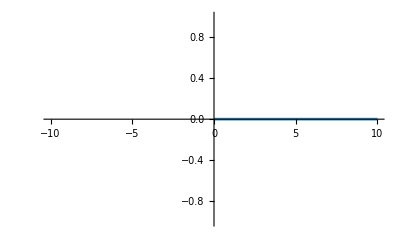

0

```mathematica
(*2.55(a)*)
equation=y[n]-1/2 y[n-1]==x[n];
eqA=y[n]/.RSolve[{equation/.x[n]->DiracDelta[n],y[0]==0},y[n],n]//First
y[n]/.RSolve[{equation,y[0]==0},y[n],n]//First
eqA/.n->0
```